```mathematica
ClearAll[z,y];
logkC1:=-5;
O20:=0.3;
H0:=70;
kC1:=10^(logkC1+3);
O10:=1-O20;
t0:=1/H0;
f[x_]=NDSolveValue[{z''[t]==(H0^4*kC1*O10^2*(z[t]^4+1)+3*H0^4*O10^2*z[t]^2*(2*kC1-3*z'[t])+H0^4*O10^2*z[t]^3*(4*kC1-3*z'[t])-3*H0^4*O10^2*z'[t]+5*H0^2*O10*z'[t]^3-kC1*z'[t]^4+H0^2*O10*z[t]*(4*H0^2*kC1*O10-9*H0^2*O10*z'[t]+5*z'[t]^3))/(2*H0^2*O10*(1+z[t])^2*z'[t]),z[t0]==0,z'[t0]==-H0},z[x],{t,t0,0}];
g[x_]=NDSolveValue[{2*H0^2*O10*y[t]^2*y'[t]*y''[t]+kC1*y'[t]^4-5*H0^2*O10*y[t]*y'[t]^3+3*H0^4*O10^2*y[t]^3*y'[t]-H0^4*O10^2*kC1*y[t]^4==0,y[t0]==1,y'[t0]==-H0},y[x],{t,t0,0},Method->"StiffnessSwitching"];
```

NDSolveValue::ndsz: 在 t == 0.000519866 处，步长实际上为零；可能存在奇点或者刚性系统.

NDSolveValue::ndsz: 在 t == 0.000519863 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {2.91837×10^-7} 位于插值函数的数据范围之外. 将使用外推法.

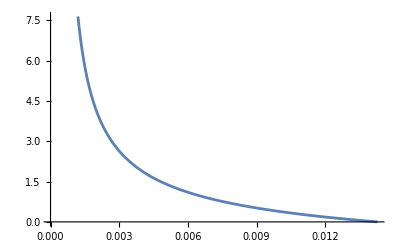

InterpolatingFunction::dmval: 输入值 {2.91837×10^-7} 位于插值函数的数据范围之外. 将使用外推法.

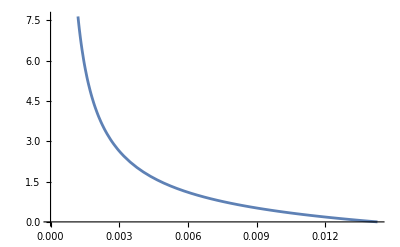

```mathematica
Plot[f[x],{x,0,t0}]
Plot[g[x]-1,{x,0,t0}]
```

```mathematica
ClearAll[H0,kC1,O10,t0];
t0=1/H0;
DSolve[{2*H0^2*O10*y[t]^2*y'[t]*y''[t]+kC1*y'[t]^4-5*H0^2*O10*y[t]*y'[t]^3+3*H0^4*O10^2*y[t]^3*y'[t]-H0^4*O10^2*kC1*y[t]^4==0,y[t0]==1,y'[t0]==-H0},y[t],t]
```

Solve::incnst: 不一致或者多余的超越方程. 在化简后，方程存在问题 1/(√O10)+(InverseFunction[-(-3 H0 Power[«2»] ArcTanh[«1»]+«1»-kC1 «1»)/(Times[«4»]+Times[«3»])&][-1/(2 «1» O10)+1])/(H0 √O10) == 0.

Solve::incnst: 不一致或者多余的超越方程. 在化简后，方程存在问题 (2 kC1)/(√O10 √(-4 kC1^2+9 H0^2 O10))+(3 H0 √O10)/(√(-4 kC1^2+9 H0^2 O10))-(3 H0^2 O10-2 kC1 InverseFunction[-Power[«2»] Plus[«3»]&][-1/2 Power[«2»] Power[«2»]+1])/(H0 √O10 √(-4 kC1^2+9 H0^2 O10)) == 0.

Solve::incnst: 不一致或者多余的超越方程. 在化简后，方程存在问题 -H0^2+(InverseFunction[-(-3 H0 Power[«2»] ArcTanh[«1»]+«1»-kC1 «1»)/(Times[«4»]+Times[«3»])&][-1/(2 «1» O10)+1])^2 == 0.

General::stop: 在本次计算中，Solve::incnst 的进一步输出将被抑制.

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[t]→ⅇ^(-(H0 √O10 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10]+1/3 (-(4 kC1 ArcTanh[1/(√O10)])/(H0 √O10)-(8 kC1^2 ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))])/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))+(18 H0 √O10 ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))])/(√(-4 kC1^2+9 H0^2 O10))-(4 kC1^2 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[H0^2-H0^2 O10]-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10])))/(H0 √O10 (-4 kC1^2+9 H0^2 O10)^(3/2))+(9 H0 √O10 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[H0^2-H0^2 O10]-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10])))/((-4 kC1^2+9 H0^2 O10)^(3/2))+3 Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10]))))/((-4 kC1^2+9 H0^2 O10)^(3/2))+(H0 √O10 (-4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[(InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])/(H0 √O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(3 H0^2 O10-2 kC1 InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[-H0^2 O10+(InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])^2]-Log[H0^2 kC1 O10-3 H0^2 O10 InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))]+kC1 (InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])^2])))/((-4 kC1^2+9 H0^2 O10)^(3/2)))}}

```mathematica
y[t_]:=ⅇ^(-(H0 √O10 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10]+1/3 (-(4 kC1 ArcTanh[1/(√O10)])/(H0 √O10)-(8 kC1^2 ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))])/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))+(18 H0 √O10 ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))])/(√(-4 kC1^2+9 H0^2 O10))-(4 kC1^2 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[H0^2-H0^2 O10]-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10])))/(H0 √O10 (-4 kC1^2+9 H0^2 O10)^(3/2))+(9 H0 √O10 (4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[1/(√O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(2 H0 kC1+3 H0^2 O10)/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[H0^2-H0^2 O10]-Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10])))/((-4 kC1^2+9 H0^2 O10)^(3/2))+3 Log[H0^2 kC1+3 H0^3 O10+H0^2 kC1 O10]))))/((-4 kC1^2+9 H0^2 O10)^(3/2))+(H0 √O10 (-4 kC1 √(-4 kC1^2+9 H0^2 O10) ArcTanh[(InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])/(H0 √O10)]+2 (4 kC1^2-9 H0^2 O10) ArcTanh[(3 H0^2 O10-2 kC1 InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])/(H0 √O10 √(-4 kC1^2+9 H0^2 O10))]+3 H0 √O10 √(-4 kC1^2+9 H0^2 O10) (Log[-H0^2 O10+(InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])^2]-Log[H0^2 kC1 O10-3 H0^2 O10 InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))]+kC1 (InverseFunction[-(-3 H0 √O10 ArcTanh[#1/(H0 √O10)]+kC1 Log[-H0^2 O10+#1^2]-kC1 Log[H0^2 O10 (kC1-3 #1)+kC1 #1^2])/(-4 H0^2 kC1^2 O10+9 H0^4 O10^2)&][-t/(2 H0^2 O10)+(-4 kC1^2+9 H0^2 O10-6 H0^2 √O10 ArcTanh[1/(√O10)]-2 H0 kC1 Log[H0^2-H0^2 O10]+2 H0 kC1 Log[H0^2 kC1+H0^2 (3 H0+kC1) O10])/(2 H0^3 O10 (-4 kC1^2+9 H0^2 O10))])^2])))/((-4 kC1^2+9 H0^2 O10)^(3/2)))
```

```mathematica
H0:=70;
kC1:=10^(logkC1+3);
O10:=1-O20;
t0:=1/H0;
```

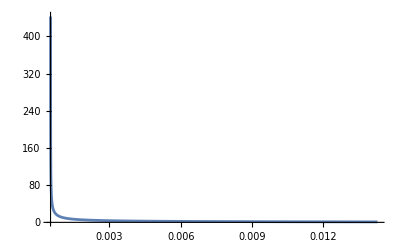

```mathematica
Plot[Re[y[t]],{t,0,t0},PlotRange->All]
```